# Test FGHVibronicCouplings function

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Codes/MathPCET

## Function (also in a new version of MathPCET package)

Fourier Grid Hamiltonian calculations of the wavefunctions, overlap integrals, and vibronic couplings (electronically nonadiabatic, electronically adiabatic, and semiclassical approximations).

FGHVibronicCouplings[file_, nGridPoints_, nStates_]

Parameters:
file - name of the file with the potential data (four columns: x(A) Ureactant(kcal/mol) Uproduct(kcal/mol) ElectronicCoupling (kcal/mol));
nGridPoints - number of grid points (should be power of two);
nStates - number of vibrational states in each well to calculate.

Options:
M -> mass of the particle in Daltons (Default - mass of the proton).

Output: Returns a nested list of the following structure:
{
{reactantEnergiesList, reactantPotentialMatrix, reactantWavefunctionsMatrix},
{productEnergiesList, productPotentialMatrix, productWavefunctionsMatrix},
overlapMatrix,
diabaticCouplingMatrix,
productCouplingMatrix,
semiclassicalCouplingMatrix,
halfTunnelingSplittingMatrix,
taueMatrix,
taupMatrix,
adiabaticityParameterMatrix,
kappaMatrix
}

where
xxxEnergiesList - is a list (vector) of length nStates;
xxxPotentialMatrix - a 2D-list (table) of the splined potential [nGridPoints × 2];
xxxWavefunctionsMatrix - a 2D-list (matrix)  [nStates × nGridPoints];
overlapMatrix - 2D-list (matrix) of overlap integrals [nStates × nStates];
diabaticCouplingMatrix - 2D-list (matrix) of vibronic couplings V_μν = <χ_μ|V(x)|χ_ν>, (kcal/mol) [nStates × nStates];
productCouplingMatrix - 2D-list (matrix) of vibronic couplings V_μν = V^el<χ_μ|χ_ν> (kcal/mol) [nStates × nStates];
semiclassicalCouplingMatrix - 2D-list (matrix) of semiclassical vibronic couplings (kcal/mol) (Georgievskii-Stuchebrukhov) [nStates × nStates];
halfTunnelingSplittingMatrix - 2D-list (matrix) of half tunneling splittings (kcal/mol) (electronically adiabatic approximation) [nStates × nStates];
taueMatrix - 2D-list (matrix) of electronic transition times (fs) [nStates × nStates];
taupMatrix - 2D-list (matrix) of proton tunneling times (fs) [nStates × nStates];
adiabaticityParameterMatrix - 2D-list (matrix) of adiabaticity parameters p [nStates × nStates];
kappaMatrix - 2D-list (matrix) of prefactors κ [nStates by nStates].

```mathematica
MassH=1.0072756064562605`15;
Dalton=1822.8900409014022`15;
FGHVibronicCouplings::inputdata="The file `1` does not exist";
FGHVibronicCouplings::noexec="Executable not found";
KappaCouplingCommand="./kappa_coupling.bin";
FGHVibronicCouplings[file_,nGridPoints_,nStates_,OptionsPattern[{M->MassH}]]:=
Module[{mass,massString,filename,nG,nS,error,command,reactantEnergies,productEnergies,reactantPotential,productPotential,reactantWavefunctions,productWavefunctions,overlapMatrix,diabCouplingMatrix,productCouplingMatrix,kappaCouplingMatrix,halfTunnelingSplittingMatrix,taueMatrix,taupMatrix,pMatrix,kappaMatrix},
filename=StringSplit[file,"."][[1]];
nG=nGridPoints;
(* Check if nStates < nGridPoints, otherwise set nStates to default value of 10 *)
If[nStates<nGridPoints,nS=nStates,nS=10];
mass=OptionValue[M]*Dalton;
massString=ToString[FortranForm[mass]];
(* run external executable to generate all the data *)
command=KappaCouplingCommand<>" "<>file<>" "<>ToString[nG]<>" "<>massString<>" "<>ToString[nS]<>" > /dev/null";
error=Run[command];
If[error!=0,Message[FGHVibronicCouplings::noexec];Abort[]];
(* Read energies from disk *)
reactantEnergies=ReadList[filename<>"_reactant_en.dat",Real];
productEnergies=ReadList[filename<>"_product_en.dat",Real];
(* Read splined potentials from disk *)
reactantPotential=ReadList[filename<>"_left.dat",Table["Real",{k,1,2+2*nS}]][[All,{1,2}]];
productPotential=Part[ReadList[filename<>"_right.dat",Table["Real",{k,1,2+2*nS}]],All,{1,2}];
(* Read wavefunctions from disk *)
reactantWavefunctions={};
productWavefunctions={};
Do[reactantWavefunctions=Append[reactantWavefunctions,Part[ReadList[filename<>"_left.dat",Table["Real",{k,1,2+2*nS}]],All,2+2*i]],{i,1,nS}];
Do[productWavefunctions=Append[productWavefunctions,Part[ReadList[filename<>"_right.dat",Table["Real",{k,1,2+2*nS}]],All,2+2*i]],{i,1,nS}];
(* Read other matrices from disk files *)
overlapMatrix=ReadList[filename<>"_overlaps.dat",Table["Real",{k,1,nS}]];
diabCouplingMatrix=ReadList[filename<>"_vibcouplings_diab.dat",Table["Real",{k,1,nS}]];
productCouplingMatrix=ReadList[filename<>"_vibcouplings_product.dat",Table["Real",{k,1,nS}]];
kappaCouplingMatrix=ReadList[filename<>"_vibcouplings_kappa.dat",Table["Real",{k,1,nS}]];
halfTunnelingSplittingMatrix=ReadList[filename<>"_tunneling_splittings.dat",Table["Real",{k,1,nS}]]/2;
taueMatrix=ReadList[filename<>"_tau_e.dat",Table["Real",{k,1,nS}]];
taupMatrix=ReadList[filename<>"_tau_p.dat",Table["Real",{k,1,nS}]];
pMatrix=ReadList[filename<>"_p_adiabaticity.dat",Table["Real",{k,1,nS}]];
kappaMatrix=ReadList[filename<>"_kappa.dat",Table["Real",{k,1,nS}]];
(* clean the data files in the current directory *)
DeleteFile[FileNames[filename<>"_*.dat"]];
(* Now gather all the results in one nested list *)
{{reactantEnergies,reactantPotential,reactantWavefunctions},{productEnergies,productPotential,productWavefunctions},overlapMatrix,diabCouplingMatrix,productCouplingMatrix,kappaCouplingMatrix,halfTunnelingSplittingMatrix,taueMatrix,taupMatrix,pMatrix,kappaMatrix}
];
```

## Testing

```mathematica
testSolution=FGHVibronicCouplings["potential.dat",512,5];
```

```mathematica
potentialLeft=testSolution⟦1⟧⟦2⟧;
potentialRight=testSolution⟦2,2⟧;
```

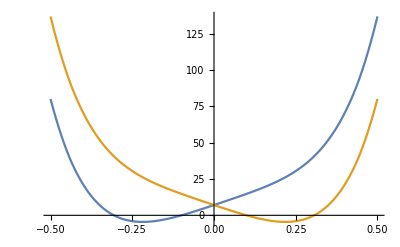

```mathematica
ListLinePlot[{potentialLeft,potentialRight}]
```

```mathematica
energiesLeft=testSolution⟦1,1⟧
energiesRight=testSolution⟦2,1⟧
```

{0.,8.44475,16.1488,23.5091,30.9731}

{0.,8.44479,16.1488,23.5091,30.9732}

```mathematica
waveFunctionsLeft=testSolution⟦1,3⟧;
waveFunctionsRight=testSolution⟦2,3⟧;
```

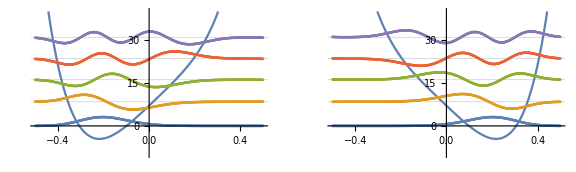

```mathematica
GraphicsRow[{
Show[
ListLinePlot[potentialLeft,PlotRange->{-10,40},GridLines->{None,energiesLeft}],
ListPlot[Table[waveFunctionsLeft⟦i⟧,{i,1,5}],DataRange->{-0.5,0.5}]
],
Show[
ListLinePlot[potentialRight,PlotRange->{-10,40},GridLines->{None,energiesRight}],
ListPlot[Table[waveFunctionsRight⟦i⟧,{i,1,5}],DataRange->{-0.5,0.5}]
]
},ImageSize->Large]
```

```mathematica
overlaps=testSolution⟦3⟧//TableForm
```

0.0560791 | 0.195447 | 0.410527 | -0.559661 | 0.529881
-0.195447 | -0.431651 | -0.491524 | 0.192236 | 0.23261
-0.410528 | -0.491524 | -0.103129 | -0.335979 | 0.274782
0.559665 | 0.192234 | -0.335981 | 0.187275 | 0.272396
-0.52988 | 0.232617 | 0.274778 | 0.272398 | -0.189967

```mathematica
kappas=testSolution⟦11⟧//TableForm
```

0.225041 | 0.307843 | 0. | 0. | 0.
0.306299 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.

```mathematica
p=testSolution⟦10⟧//TableForm
```

0.00882905 | 0.0176652 | 0. | 0. | 0.
0.0174637 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.

```mathematica
productCouplings=testSolution⟦5⟧//TableForm
```

0.0699432 | 0.274909 | 0.752455 | 1.3873 | 1.76382
0.274942 | 0.538364 | 0.67602 | 0.337223 | 0.552048
0.752432 | 0.676113 | 0.128624 | 0.458848 | 0.476848
1.38732 | 0.337207 | 0.458915 | 0.233574 | 0.372013
1.76368 | 0.552077 | 0.476823 | 0.372068 | 0.236931

```mathematica
semiclassicalCouplings=testSolution⟦6⟧//TableForm
```

0.758482 | 0.295897 | 0. | 0. | 0.
0.294412 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.

```mathematica
halfTunnelingCouplings=testSolution⟦7⟧//TableForm
```

3.37041 | 0.961194 | 0. | 0. | 0.
0.961194 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.